```mathematica
democrats =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"-democratic-party-platform"], Length[#] > 0 &]];
```

```mathematica
demtexts =StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""], 21;;-1] & /@ democrats[[1;;31]];
```

```mathematica
demkeys = Table[StringJoin[ToString[2024 - 4*i], " Democratic Party"], {i, Range[Length[demtexts]]}];
```

```mathematica
democratTexts =Association[Table[demkeys[[i]] -> demtexts[[i]], {i, Range[Length[demtexts]]}]];
```

```mathematica
republicans =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"republican-party-platform"~~___], Length[#] > 0 &]];
```

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],21;;-1] & /@ republicans[[2;;31]];
```

```mathematica
repkeys = Table[StringJoin[ToString[2020 - 4*i], " Republican Party"], {i, Range[Length[reptexts]]}];
```

```mathematica
republicanTexts =Association[Table[repkeys[[i]] -> reptexts[[i]], {i, Range[Length[reptexts]]}]];
```

```mathematica
alltexts = Join[democratTexts, republicanTexts]
```

```mathematica
partycolors[p_] := If[StringTake[p, 6;;-1]=="Republican Party", Red, Blue]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[alltexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[alltexts], Keys[alltexts]}], ImageSize->Full, PlotRangePadding->{10, 100}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[democratTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[democratTexts], Keys[democratTexts]}], ImageSize->Full, PlotRangePadding->{10, 160}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[republicanTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[republicanTexts], Keys[republicanTexts]}], ImageSize->Full, PlotRangePadding->{10, 60}]]
```

```mathematica
republicanNominee = {"Trump","Trump","Romney","McCain","Bush","Bush","Dole","Bush","Bush","Reagan","Reagan","Ford","Nixon","Nixon","Goldwater","Nixon","Eisenhower","Eisenhower","Dewey","Dewey","Willkie","Landon","Hoover","Hoover","Coolidge","Harding","Hughes","Taft","Taft","Roosevelt","McKinley"};
```

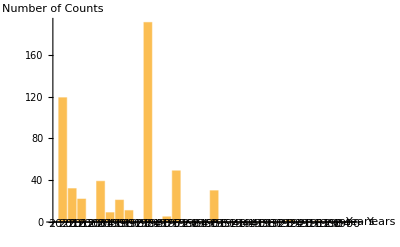

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[democratTexts], republicanNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[democratTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
democratNominee = {"Clinton", "Obama", "Obama", "Kerry", "Gore", "Clinton", "Clinton", "Dukakis", "Mondale", "Carter", "Carter", "McGovern", "Humphrey", "Johnson", "Kennedy", "Stevenson","Stevenson", "Truman", "Roosevelt", "Roosevelt", "Roosevelt", "Roosevelt", "Smith", "Davis", "Cox", "Wilson", "Wilson", "Bryan", "Parker", "Bryan"};
```

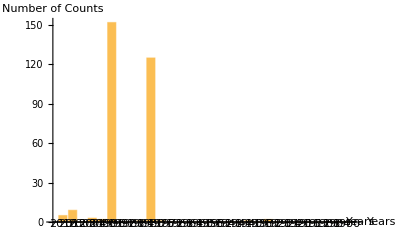

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[republicanTexts], democratNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[republicanTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
posnegtrain = ResourceData["Sample Data: Movie Review Sentence Polarity", "TrainingData"]
```

```mathematica
(*Let's think abt this*)
```

```mathematica
sentimentScore[text_,device_:"CPU"]:=With[{output=NetModel["Sentiment Language Model Trained on Amazon Product Review Data"][text,NetPort[{"LastState","Output"}],TargetDevice->device]},Switch[Depth[output],2,output[[2389]],3,output[[All,2389]]]]
```

```mathematica
testingS= TextSentences[Values[democratTexts][[1]]];
```

```mathematica
Round[Length[testingS]/4]
```

381

```mathematica
test = sentimentScore[RandomSample[testingS, Round[Length[testingS]/4]]]
```

{-0.00747268,0.185457,-0.0448015,0.105684,-0.00492656,0.270831,0.0843057,0.0331736,0.0577343,-0.178358,0.110497,0.117044,0.0525235,-0.124325,-0.000695527,0.234273,-0.0236105,-0.0151935,0.00983343,0.11147,0.00214194,0.0780388,0.0904976,0.134854,0.0254708,0.03251,0.216193,0.0452698,0.0288904,0.0655274,0.0423241,0.0718917,0.169498,0.100279,0.0583303,0.0687782,-0.00646307,0.0856719,0.0195671,0.0127744,0.0979863,0.0682817,0.111462,-0.0673442,0.281165,0.0430131,-0.00650196,-0.0328146,-0.0843535,0.172737,0.0644661,0.0819325,0.087286,0.142092,-0.0554318,0.131447,0.147917,0.199525,-0.242181,0.066461,0.0317331,0.0466431,0.0450903,0.0552796,-0.112375,0.0261053,-0.0280839,-0.0100152,0.0112271,0.0698559,0.234289,0.00533234,-0.116792,0.118044,0.0708352,0.00637824,0.0570534,0.0128576,-0.00212767,0.00757591,0.0365533,0.02891,0.0120802,0.0455807,0.115472,0.0100767,-0.0039585,0.0813143,0.0381061,-0.025563,0.153769,0.10672,0.0603088,0.0890397,0.104842,0.0714661,0.0932287,0.032389,-0.179061,0.022683,0.0279399,-0.0177079,-0.0923431,0.186598,0.0651812,0.0780881,0.124338,0.0512708,0.106862,-0.0196925,-0.00729101,-0.0625948,0.0944565,-0.0778112,-0.0452823,0.0467575,0.0256496,0.1583,0.0417923,0.0785766,-0.0978214,0.151882,0.0902661,-0.188041,0.046245,0.0065309,0.273282,0.163697,-0.0408155,0.0931815,0.0584907,0.0318373,0.105581,-0.0583478,-0.102808,0.201813,0.0373944,0.154943,-0.116522,0.114535,-0.00068031,0.16826,0.0905155,0.0926814,0.0188669,0.0558287,0.168204,0.0861531,0.0342375,0.0568093,0.00118352,0.0272153,-0.0345553,0.0288949,0.0484331,0.0466485,-0.0268972,-0.0413435,0.00223308,-0.00481465,-0.0498007,0.226712,0.143987,0.142493,0.0211318,0.121562,0.0597125,0.0805411,-0.0364234,0.00428365,0.0736808,-0.0324109,0.0721595,0.0903891,0.063898,0.0653489,-0.00895649,0.0709965,0.495399,0.103069,0.0292959,-0.156419,0.120481,0.00989723,0.0762764,-0.0413977,-0.135166,0.0267112,0.116182,0.0999975,0.176153,0.0862803,0.0294467,-0.00935676,0.0652861,0.0480214,0.143527,0.00662928,-0.0134172,0.0749874,0.0456598,0.129571,0.0362118,-0.0306162,-0.0267658,0.162637,0.0941352,-0.123651,-0.126885,-0.0399128,-0.0117556,0.136942,0.0833113,0.0118054,0.00760659,-0.0842353,0.0578134,-0.0357515,0.0825248,0.130769,-0.0358518,0.0149562,0.150325,0.0814283,0.0786847,0.160922,0.105679,-0.0610644,0.1086,0.140208,-0.0218939,0.00144277,0.0823949,0.0263377,0.0688798,-0.485905,0.0670969,0.0191592,0.0889714,0.0480958,0.0426712,-0.0414306,0.0780246,0.00860539,0.296546,0.302346,0.0232236,-0.0175717,0.0528646,0.158787,0.138373,0.260245,-0.0387733,0.0494935,0.144523,0.143795,-0.1436,0.106465,0.040364,0.0687098,-0.0378498,0.148461,0.337793,0.307436,-0.0605173,0.0162776,-0.0487035,0.0574483,0.0503167,0.0466007,-0.0699352,0.238249,0.0130802,0.118434,0.353582,0.09828,0.0050577,0.040247,0.108711,0.0442184,-0.12866,0.0737751,0.113275,0.0406067,0.0204157,0.101769,0.239421,0.296234,0.0425529,0.130654,0.0745788,-0.000222033,0.0252021,0.0305765,0.199225,0.0816937,0.00764544,0.173701,-0.199173,0.0585708,0.433964,0.100005,-0.0207744,0.013258,0.177242,-0.0253445,0.0990056,-0.0563031,-0.0103321,0.0525497,0.20402,0.0339861,-0.0280573,0.0335572,0.119967,0.213163,0.0177445,0.0907216,-0.0317529,0.0710135,0.061882,0.0451308,0.055189,-0.106138,0.0638673,0.0800016,0.221631,0.0443415,0.0329152,-0.014092,0.468592,0.117851,0.087681,0.0193739,-0.011791,-0.00156347,0.116513,0.187415,0.209919,0.0501614,-0.166856,0.0228393,0.0793903,0.0720503,0.0411948,0.0537352,0.0304168,0.0203082,0.0452395,-0.00055558,-0.0247204,0.0351788,0.0693459,0.156042,0.0623433,0.220573,0.111639,0.0234418,0.183462,0.126324,-0.0469513,-0.0266695,0.11291,-0.0116902,0.106437,-0.0119265,-0.0948354,-0.0489917,0.0977125,0.172934,0.0918723,0.0784887,0.204136,0.0492339,0.0625359,0.122381,0.0906612,0.186843,0.0211075,0.0608071,0.0931878}

```mathematica
Mean[Table[sentimentScore[s], {s, RandomSample[TextSentences[Values[democratTexts][[1]]], 200]}]]
```

$Aborted

```mathematica
(*up to here*)
```

```mathematica
neutPart = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/political_social_media.csv", "Data", HeaderLines->1]
```

```mathematica
classNeutPart = Table[StringReplace[ToString[s[[21]]], PunctuationCharacter:>""]->s[[8]], {s, neutPart}]
```

```mathematica
indices=RandomSample[Range[Length[libcons]],Min[subsetSize,Length[libcons]]];
```

```mathematica
datasetDown=Values[Keys/@GroupBy[Thread[DimensionReduce[Keys[classlibcons],2,Method->"TSNE"]->Values[classlibcons]],Values]];
```

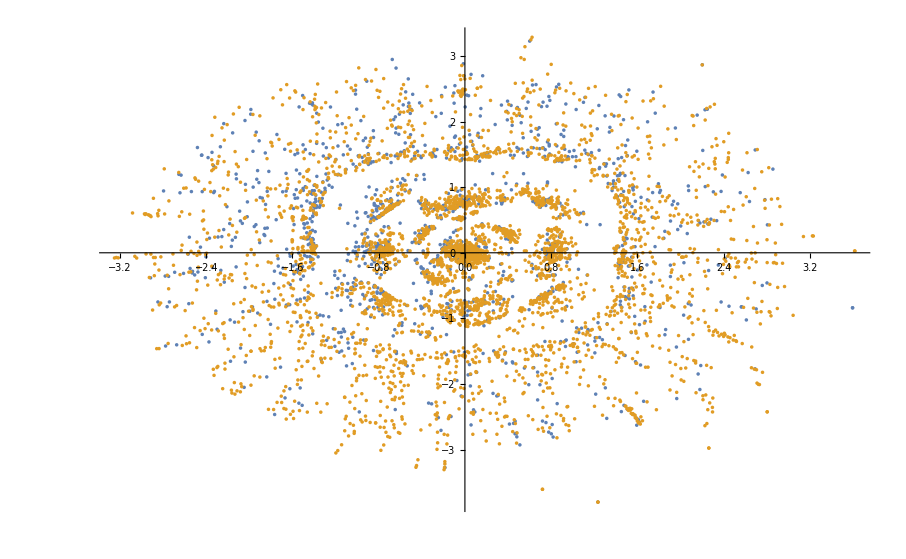

```mathematica
ListPlot[datasetDown]
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][classNeutPart];
```

```mathematica
neutPartF = Classify[classNeutPart, Method->"RandomForest"]
```

ClassifierFunction[…]

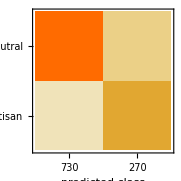
Classifier Measurements
Classifier method | Markov
Number of test examples | 1000
Accuracy | (94.30.7) %
Accuracy baseline | (76.51.3) %
Geometric mean of probabilities | 0.774 ± 0.035
Mean cross entropy | 0.256 ± 0.045
Single evaluation time | 2.47 ms/example
Batch evaluation speed | 2.94 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[neutPartF,testSet]
```

```mathematica
demPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[democratTexts]
```

{0.703211,0.696444,0.658335,0.654036,0.598425,0.647225,0.664165,0.598313,0.720076,0.698671,0.641517,0.710451,0.722308,0.600104,0.620425,0.671227,0.699819,0.599839,0.62437,0.557367,0.692662,0.616512,0.706971,0.734935,0.703282,0.715068,0.710106,0.786173,0.786319,0.806267,0.79256}

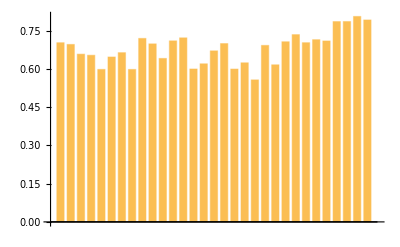

```mathematica
BarChart[demPartisanCount]
```

```mathematica
repPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[republicanTexts]
```

{0.708057,0.684293,0.65792,0.567213,0.663928,0.689252,0.658059,0.631696,0.63709,0.703443,0.669713,0.622125,0.622125,0.696871,0.632323,0.590069,0.717187,0.643967,0.662785,0.74188,0.675587,0.708868,0.68367,0.705545,0.782417,0.813895,0.746157,0.711108,0.741839,0.668466}

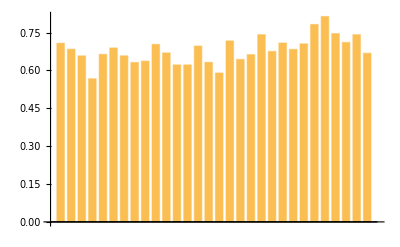

```mathematica
BarChart[repPartisanCount]
```

```mathematica
partisanCount = Counts[libconsf[TextSentences[#]]]&/@ Values[democratTexts]
```

{<|neutral→444,partisan→1081|>,<|partisan→742,neutral→307|>,<|partisan→732,neutral→352|>,<|neutral→366,partisan→744|>,<|partisan→576,neutral→364|>,<|partisan→755,neutral→378|>,<|neutral→270,partisan→563|>,<|partisan→220,neutral→144|>,<|partisan→52,neutral→19|>,<|partisan→1178,neutral→477|>,<|partisan→1056,neutral→574|>,<|neutral→236,partisan→623|>,<|partisan→662,neutral→232|>,<|neutral→257,partisan→402|>,<|partisan→538,neutral→315|>,<|partisan→540,neutral→244|>,<|partisan→384,neutral→155|>,<|neutral→143,partisan→227|>,<|partisan→104,neutral→63|>,<|neutral→35,partisan→46|>,<|neutral→52,partisan→132|>,<|neutral→34,partisan→54|>,<|partisan→31,neutral→14|>,<|partisan→152,neutral→50|>,<|partisan→162,neutral→62|>,<|partisan→139,neutral→50|>,<|partisan→96,neutral→41|>,<|partisan→99,neutral→25|>,<|partisan→84,neutral→22|>,<|partisan→68,neutral→16|>,<|partisan→60,neutral→14|>}

```mathematica
(*Bad*)
```

```mathematica
libCon = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/master_df.csv", "Data", HeaderLines->1]
```

```mathematica
removeSet = {"a","about","above","across","after","afterwards","again","against","all","almost","alone","along","already","also","although","always","am","among","amongst","amoungst","amount","amp","an","and","another","any","anyhow","anyone","anything","anyway","anywhere","are","around","as","at","back","be","became","because","become","becomes","becoming","been","before","beforehand","behind","being","below","beside","besides","between","beyond","bill","both","bottom","but","by","call","can","cannot","cant","co","com","con","could","couldnt","cry","de","describe","detail","did","do","does","done","down","due","during","each","eg","eight","either","eleven","else","elsewhere","empty","enough","etc","even","ever","every","everyone","everything","everywhere","except","few","fifteen","fifty","fill","find","fire","first","five","for","former","formerly","forty","found","four","from","front","full","further","get","give","go","had","has","hasnt","have","he","hence","her","here","hereafter","hereby","herein","hereupon","hers","herself","him","himself","his","how","however","https","hundred","i","ie","if","in","inc","indeed","interest","into","is","it","its","itself","just","keep","last","latter","latterly","least","less","like","ltd","made","many","may","me","meanwhile","might","mill","mine","more","moreover","most","mostly","move","much","must","my","myself","name","namely","neither","never","nevertheless","next","nine","no","nobody","none","noone","nor","not","nothing","now","nowhere","of","off","often","on","once","one","only","onto","or","other","others","otherwise","our","ours","ourselves","out","over","own","part","per","perhaps","please","put","rather","re","same","say","says","see","seem","seemed","seeming","seems","serious","several","she","should","show","side","since","sincere","six","sixty","so","some","somehow","someone","something","sometime","sometimes","somewhere","still","such","system","take","ten","than","that","the","their","them","themselves","then","thence","there","thereafter","thereby","therefore","therein","thereupon","these","they","thick","thin","things","third","this","those","though","three","through","throughout","thru","thus","to","together","too","top","toward","towards","twelve","twenty","two","un","under","until","up","upon","us","very","via","want","was","watch","we","well","were","what","whatever","when","whence","whenever","where","whereafter","whereas","whereby","wherein","whereupon","wherever","whether","which","while","whither","who","whoever","whole","whom","whose","why","will","with","within","without","would","www","x200b","yet","you","your","yours","yourself","yourselves"};
```

```mathematica
classLibCon = Table[StringReplace[StringJoin[Riffle[TextWords[ToString[s[[3]]]]/. Table[w->"",{w, removeSet}], " "]], PunctuationCharacter:>""]->If[s[[4]]==0, "Conservative", "Liberal"], {s, libCon}];
```

```mathematica
classLibCon = Table[StringReplace[DeleteStopwords[ToString[s[[3]]]], PunctuationCharacter:>""]->If[s[[4]]==0, "Conservative", "Liberal"], {s, libCon}];
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][classLibCon];
```

```mathematica
libConF = Classify[trainSet]
```

ClassifierFunction[…]

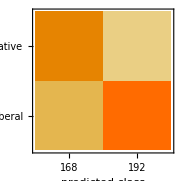
Classifier Measurements
Classifier method | Markov
Number of test examples | 360
Accuracy | (71.12.4) %
Accuracy baseline | (55.62.6) %
Geometric mean of probabilities | 0.336 ± 0.041
Mean cross entropy | 1.09 ± 0.12
Single evaluation time | 2.43 ms/example
Batch evaluation speed | 3.23 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[libConF, testSet]
```

```mathematica
libConF = Classify[classLibCon]
```

ClassifierFunction[…]

```mathematica
Counts[libConF[TextSentences[Values[democratTexts][[1]]]]]
```

<|Conservative→1429,Liberal→96|>

```mathematica
testing = Mean[Table[ps["Liberal"],{ps,libConF[TextSentences[#], "Probabilities"]}]] & /@ Values[democratTexts]
```

{0.0906621,0.134686,0.106296,0.108966,0.130673,0.0964915,0.112803,0.0777427,0.0351542,0.0935322,0.0894019,0.0916777,0.0824136,0.076665,0.0430849,0.0780739,0.0827304,0.066213,0.070371,0.0846131,0.0574465,0.0386614,0.00867073,0.0424787,0.0356201,0.0219026,0.052286,0.0139061,0.0154346,0.00471323,0.0222954}

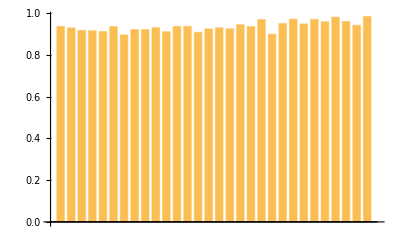

```mathematica
BarChart[testing]
```

```mathematica
(*up to here*)
```

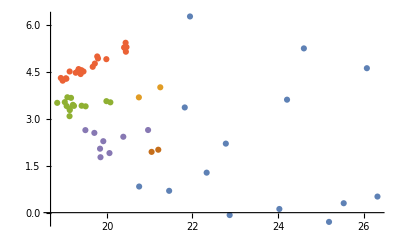

```mathematica
ListPlot[MapThread[FindClusters[DimensionReduce[Values[alltexts], Method->"UMAP"], Method->"DBSCAN"]]
```